```mathematica
ClearAll["Global`*"]
```

```mathematica
(*For ϵ=-0.57%*)
```

```mathematica
TvsCp10:={{0.9955456570155903,0.12559055118110238},{1.0723830734966593,0.12322834645669292},{1.1391982182628064,0.1220472440944882},{1.2260579064587973,0.12244094488188978},{1.2861915367483299,0.12283464566929136},{1.3897550111358576,0.12480314960629921},{1.489977728285078,0.12755905511811022},{1.5734966592427617,0.12992125984251968},{1.6603563474387528,0.13425196850393703},{1.7438752783964364,0.13740157480314963},{1.8173719376391984,0.14212598425196854},{1.8875278396436528,0.14645669291338584},{1.9643652561247216,0.15118110236220475},{2.041202672605791,0.15551181102362205},{2.1247216035634744,0.16141732283464572},{2.198218262806236,0.16614173228346457},{2.2616926503340755,0.17244094488188977},{2.3351893095768372,0.17755905511811026},{2.4020044543429844,0.1830708661417323},{2.4788418708240534,0.19015748031496063},{2.552338530066815,0.19606299212598427},{2.6158129175946545,0.20118110236220474},{2.675946547884187,0.20748031496062994},{2.7227171492204896,0.212992125984252},{2.799554565701559,0.21968503937007877},{2.859688195991091,0.2267716535433071},{2.9398663697104674,0.23464566929133862},{3.0066815144766146,0.2409448818897638},{3.0801781737193763,0.24645669291338584},{3.1570155902004453,0.2547244094488189},{3.2037861915367483,0.2618110236220473},{3.2639198218262804,0.2661417322834646},{3.307349665924276,0.27125984251968505},{3.367483296213808,0.27716535433070866},{3.430957683741648,0.28188976377952757}}
```

```mathematica
TvsCp10[[4]][[1]]
```

1.22606

```mathematica
Length[TvsCp10]
```

35

```mathematica
T10=Range[Length[TvsCp10]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35}

```mathematica
Cp10=Range[Length[TvsCp10]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35}

```mathematica
For[i=1,i<=Length[TvsCp10],i++,T10[[i]]=TvsCp10[[i]][[1]];Cp10[[i]]=TvsCp10[[i]][[2]]]
```

```mathematica
Length[T10]
```

35

```mathematica
T10
```

{0.995546,1.07238,1.1392,1.22606,1.28619,1.38976,1.48998,1.5735,1.66036,1.74388,1.81737,1.88753,1.96437,2.0412,2.12472,2.19822,2.26169,2.33519,2.402,2.47884,2.55234,2.61581,2.67595,2.72272,2.79955,2.85969,2.93987,3.00668,3.08018,3.15702,3.20379,3.26392,3.30735,3.36748,3.43096}

```mathematica
Cp10
```

{0.125591,0.123228,0.122047,0.122441,0.122835,0.124803,0.127559,0.129921,0.134252,0.137402,0.142126,0.146457,0.151181,0.155512,0.161417,0.166142,0.172441,0.177559,0.183071,0.190157,0.196063,0.201181,0.20748,0.212992,0.219685,0.226772,0.234646,0.240945,0.246457,0.254724,0.261811,0.266142,0.27126,0.277165,0.28189}

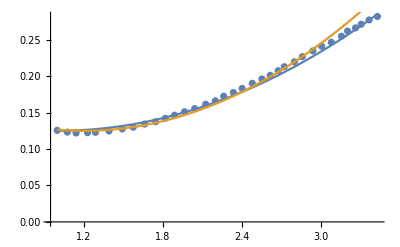

```mathematica
plt101=ListPlot[Transpose@{T10,Cp10}];(*Cp vs temp*)
plt102=Plot[{0.125+0.027*(x-T10[[1]])^2,0.125+0.037*(x-1.2)^2},{x,T10[[1]],T10[[Length[T10]]]}];
Show[plt101,plt102]
```

```mathematica
(*For ϵ=-0.53%*)
```

```mathematica
TvsCp9:={{1.002227171492205,0.13070866141732285},{1.0657015590200447,0.12874015748031495},{1.1492204899777285,0.12716535433070866},{1.2427616926503342,0.12755905511811022},{1.356347438752784,0.12795275590551183},{1.4565701559020043,0.1303149606299213},{1.546770601336303,0.13346456692913386},{1.6336302895322943,0.13700787401574804},{1.7171492204899779,0.14015748031496064},{1.7806236080178175,0.14409448818897638},{1.854120267260579,0.14763779527559057},{1.9342984409799555,0.15196850393700786},{2.014476614699332,0.15708661417322836},{2.0946547884187083,0.16181102362204727},{2.1547884187082404,0.16653543307086613},{2.2349665924276167,0.17244094488188977},{2.2817371937639197,0.17598425196850395},{2.3719376391982183,0.18110236220472445},{2.4320712694877504,0.18740157480314962},{2.505567928730512,0.19488188976377954},{2.5723830734966593,0.2},{2.645879732739421,0.20590551181102362},{2.732739420935412,0.21417322834645672},{2.8028953229398663,0.2192913385826772},{2.8663697104677057,0.22637795275590553},{2.916481069042316,0.23031496062992127},{2.969933184855234,0.23464566929133862},{3.0334075723830733,0.23976377952755906},{3.0734966592427617,0.24488188976377956},{3.1403118040089084,0.24803149606299213},{3.21380846325167,0.24921259842519689}}
```

```mathematica
TvsCp9[[4]][[1]]
```

1.24276

```mathematica
Length[TvsCp9]
```

31

```mathematica
T9=Range[Length[TvsCp9]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
Cp9=Range[Length[TvsCp9]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
For[i=1,i<=Length[TvsCp9],i++,T9[[i]]=TvsCp9[[i]][[1]];Cp9[[i]]=TvsCp9[[i]][[2]]]
```

```mathematica
Length[T9]
```

31

```mathematica
T9
```

{1.00223,1.0657,1.14922,1.24276,1.35635,1.45657,1.54677,1.63363,1.71715,1.78062,1.85412,1.9343,2.01448,2.09465,2.15479,2.23497,2.28174,2.37194,2.43207,2.50557,2.57238,2.64588,2.73274,2.8029,2.86637,2.91648,2.96993,3.03341,3.0735,3.14031,3.21381}

```mathematica
Cp9
```

{0.130709,0.12874,0.127165,0.127559,0.127953,0.130315,0.133465,0.137008,0.140157,0.144094,0.147638,0.151969,0.157087,0.161811,0.166535,0.172441,0.175984,0.181102,0.187402,0.194882,0.2,0.205906,0.214173,0.219291,0.226378,0.230315,0.234646,0.239764,0.244882,0.248031,0.249213}

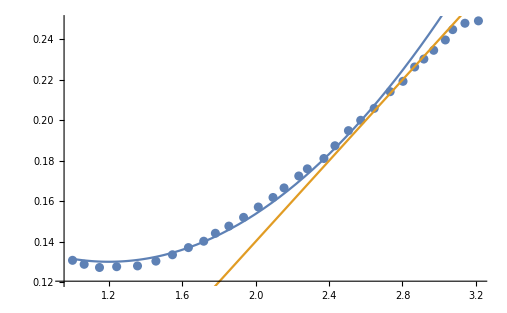

```mathematica
plt91=ListPlot[Transpose@{T9,Cp9}];(*Cp vs temp*)
plt92=Plot[{0.13+0.037*(x-1.2)^2,0.19+0.1*(x-2.5)},{x,T9[[1]],T9[[Length[T9]]]}];
Show[plt91,plt92]
```

```mathematica
(*For ϵ=-0.50%*)
```

```mathematica
TvsCp8:={{1.0055679287305124,0.13818897637795277},{1.0523385300668153,0.13622047244094487},{1.1057906458797329,0.13385826771653542},{1.1659242761692652,0.13385826771653542},{1.2193763919821827,0.13425196850393703},{1.279510022271715,0.13385826771653542},{1.3396436525612474,0.13385826771653542},{1.4097995545657016,0.13543307086614176},{1.4632516703786194,0.13661417322834646},{1.516703786191537,0.13858267716535436},{1.5668151447661471,0.13976377952755908},{1.6302895322939868,0.14212598425196854},{1.690423162583519,0.144488188976378},{1.7505567928730512,0.1468503937007874},{1.8140311804008908,0.15000000000000002},{1.8674832962138086,0.15275590551181104},{1.9175946547884188,0.15590551181102363},{1.9643652561247216,0.15866141732283465},{2.0044543429844097,0.1610236220472441},{2.0378619153674835,0.16417322834645673},{2.0779510022271714,0.16574803149606301},{2.1180400890868594,0.16850393700787403},{2.1547884187082404,0.17086614173228348},{2.194877505567929,0.17440944881889767},{2.2349665924276167,0.1767716535433071},{2.275055679287305,0.17913385826771655},{2.315144766146993,0.18228346456692918},{2.3552338530066814,0.18503937007874016},{2.388641425389755,0.18858267716535435},{2.4253897550111354,0.1921259842519685},{2.465478841870824,0.19527559055118113},{2.5122494432071267,0.1988188976377953},{2.5590200445434297,0.20236220472440947},{2.6057906458797326,0.2062992125984252},{2.655902004454343,0.21023622047244095},{2.702672605790646,0.21417322834645672},{2.7427616926503338,0.21653543307086617},{2.779510022271715,0.22007874015748033},{2.8195991091314028,0.22322834645669293},{2.8630289532293984,0.2251968503937008},{2.903118040089087,0.2279527559055118},{2.9599109131403116,0.22952755905511812},{3.0033407572383073,0.23070866141732285}}
```

```mathematica
TvsCp8[[4]][[1]]
```

1.16592

```mathematica
Length[TvsCp8]
```

43

```mathematica
T8=Range[Length[TvsCp8]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43}

```mathematica
Cp8=Range[Length[TvsCp8]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43}

```mathematica
For[i=1,i<=Length[TvsCp8],i++,T8[[i]]=TvsCp8[[i]][[1]];Cp8[[i]]=TvsCp8[[i]][[2]]]
```

```mathematica
Length[T8]
```

43

```mathematica
T8
```

{1.00557,1.05234,1.10579,1.16592,1.21938,1.27951,1.33964,1.4098,1.46325,1.5167,1.56682,1.63029,1.69042,1.75056,1.81403,1.86748,1.91759,1.96437,2.00445,2.03786,2.07795,2.11804,2.15479,2.19488,2.23497,2.27506,2.31514,2.35523,2.38864,2.42539,2.46548,2.51225,2.55902,2.60579,2.6559,2.70267,2.74276,2.77951,2.8196,2.86303,2.90312,2.95991,3.00334}

```mathematica
Cp8
```

{0.138189,0.13622,0.133858,0.133858,0.134252,0.133858,0.133858,0.135433,0.136614,0.138583,0.139764,0.142126,0.144488,0.14685,0.15,0.152756,0.155906,0.158661,0.161024,0.164173,0.165748,0.168504,0.170866,0.174409,0.176772,0.179134,0.182283,0.185039,0.188583,0.192126,0.195276,0.198819,0.202362,0.206299,0.210236,0.214173,0.216535,0.220079,0.223228,0.225197,0.227953,0.229528,0.230709}

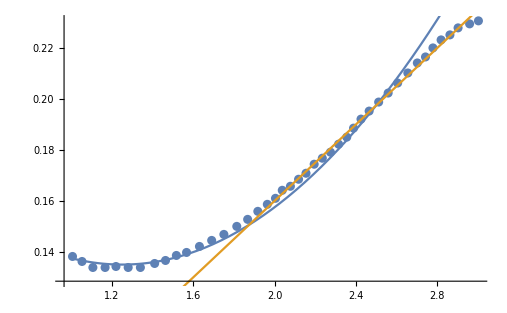

```mathematica
plt81=ListPlot[Transpose@{T8,Cp8}];(*Cp vs temp*)
plt82=Plot[{0.135+0.04*(x-1.25)^2,0.16+0.075(x-2)},{x,T8[[1]],T8[[Length[T8]]]}];
Show[plt81,plt82]
```

```mathematica
(*For ϵ=-0.48%*)
```

```mathematica
TvsCp7:={{1.0089086859688197,0.14803149606299212},{1.0489977728285078,0.1452755905511811},{1.099109131403118,0.14330708661417327},{1.1525612472160358,0.14173228346456693},{1.2293986636971048,0.14212598425196854},{1.3095768374164813,0.14212598425196854},{1.3830734966592428,0.1425196850393701},{1.4498886414253898,0.14409448818897638},{1.5033407572383073,0.14566929133858267},{1.5835189309576836,0.14803149606299212},{1.6737193763919822,0.15118110236220475},{1.747216035634744,0.15354330708661418},{1.8073496659242763,0.15708661417322836},{1.8808463251670378,0.16141732283464572},{1.9443207126948776,0.16417322834645673},{2.0044543429844097,0.16850393700787403},{2.0612472160356345,0.17125984251968504},{2.114699331848552,0.17480314960629922},{2.178173719376392,0.178740157480315},{2.2383073496659245,0.18228346456692918},{2.2984409799554566,0.18700787401574803},{2.3552338530066814,0.19055118110236222},{2.408685968819599,0.19527559055118113},{2.4621380846325165,0.19921259842519687},{2.5122494432071267,0.20236220472440947},{2.5690423162583516,0.2062992125984252},{2.622494432071269,0.21102362204724412},{2.675946547884187,0.21496062992125986},{2.7193763919821827,0.21574803149606303},{2.769487750556793,0.21692913385826773}}
```

```mathematica
TvsCp7[[4]][[1]]
```

1.15256

```mathematica
Length[TvsCp7]
```

30

```mathematica
T7=Range[Length[TvsCp7]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
Cp7=Range[Length[TvsCp7]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
For[i=1,i<=Length[TvsCp7],i++,T7[[i]]=TvsCp7[[i]][[1]];Cp7[[i]]=TvsCp7[[i]][[2]]]
```

```mathematica
Length[T7]
```

30

```mathematica
T7
```

{1.00891,1.049,1.09911,1.15256,1.2294,1.30958,1.38307,1.44989,1.50334,1.58352,1.67372,1.74722,1.80735,1.88085,1.94432,2.00445,2.06125,2.1147,2.17817,2.23831,2.29844,2.35523,2.40869,2.46214,2.51225,2.56904,2.62249,2.67595,2.71938,2.76949}

```mathematica
Cp7
```

{0.148031,0.145276,0.143307,0.141732,0.142126,0.142126,0.14252,0.144094,0.145669,0.148031,0.151181,0.153543,0.157087,0.161417,0.164173,0.168504,0.17126,0.174803,0.17874,0.182283,0.187008,0.190551,0.195276,0.199213,0.202362,0.206299,0.211024,0.214961,0.215748,0.216929}

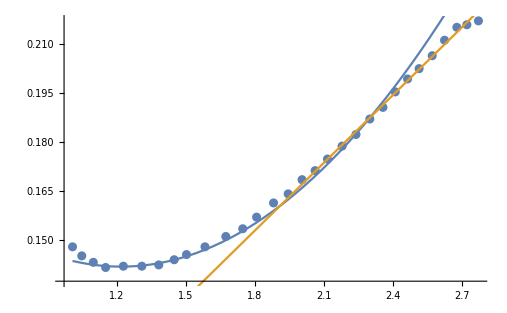

```mathematica
plt71=ListPlot[Transpose@{T7,Cp7}];(*Cp vs temp*)
plt72=Plot[{0.142+0.039*(x-1.22)^2,0.1875+0.069(x-2.3)},{x,T7[[1]],T7[[Length[T7]]]}];
Show[plt71,plt72]
```

```mathematica
(*For ϵ=-0.44%*)
```

```mathematica
TvsCp6:={{1.0055679287305124,0.16220472440944883},{1.0322939866369711,0.15944881889763782},{1.079064587973274,0.15708661417322836},{1.1291759465478843,0.1551181102362205},{1.1993318485523385,0.1551181102362205},{1.2661469933184857,0.15433070866141732},{1.3429844097995547,0.15433070866141732},{1.4265033407572383,0.15590551181102363},{1.506681514476615,0.15748031496062992},{1.576837416481069,0.15905511811023623},{1.6570155902004455,0.16181102362204727},{1.747216035634744,0.1645669291338583},{1.8307349665924275,0.1692913385826772},{1.9142538975501113,0.17322834645669294},{1.9910913140311803,0.17795275590551182},{2.074610244988864,0.18228346456692918},{2.1280623608017817,0.18582677165354333},{2.1915367483296215,0.1889763779527559},{2.2416481069042318,0.19173228346456694},{2.2984409799554566,0.19488188976377954},{2.338530066815145,0.19842519685039373},{2.3819599109131406,0.20078740157480318},{2.4387527839643655,0.20118110236220474},{2.482182628062361,0.20511811023622048}}
```

```mathematica
TvsCp6[[4]][[1]]
```

1.12918

```mathematica
Length[TvsCp6]
```

24

```mathematica
T6=Range[Length[TvsCp6]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

```mathematica
Cp6=Range[Length[TvsCp6]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

```mathematica
For[i=1,i<=Length[TvsCp6],i++,T6[[i]]=TvsCp6[[i]][[1]];Cp6[[i]]=TvsCp6[[i]][[2]]]
```

```mathematica
Length[T6]
```

24

```mathematica
T6
```

{1.00557,1.03229,1.07906,1.12918,1.19933,1.26615,1.34298,1.4265,1.50668,1.57684,1.65702,1.74722,1.83073,1.91425,1.99109,2.07461,2.12806,2.19154,2.24165,2.29844,2.33853,2.38196,2.43875,2.48218}

```mathematica
Cp6
```

{0.162205,0.159449,0.157087,0.155118,0.155118,0.154331,0.154331,0.155906,0.15748,0.159055,0.161811,0.164567,0.169291,0.173228,0.177953,0.182283,0.185827,0.188976,0.191732,0.194882,0.198425,0.200787,0.201181,0.205118}

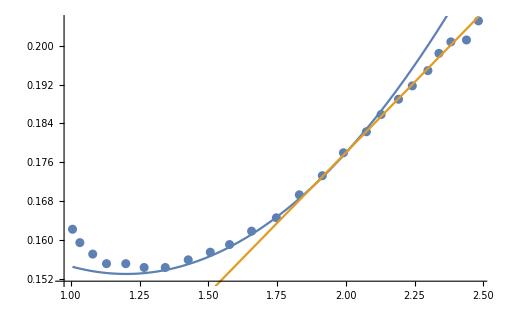

```mathematica
plt61=ListPlot[Transpose@{T6,Cp6}];(*Cp vs temp*)
plt62=Plot[{0.153+0.039*(x-1.2)^2,0.178+0.058(x-2.0)},{x,T6[[1]],T6[[Length[T6]]]}];
Show[plt61,plt62]
```

```mathematica
(*For ϵ=-0.39%*)
```

```mathematica
TvsCp5:={{1.0055679287305124,0.18267716535433073},{1.0356347438752787,0.1795275590551181},{1.069042316258352,0.17716535433070868},{1.1124721603563477,0.1751968503937008},{1.1692650334075725,0.17322834645669294},{1.2427616926503342,0.17244094488188977},{1.3129175946547886,0.17125984251968504},{1.376391982182628,0.1720472440944882},{1.4565701559020043,0.1720472440944882},{1.510022271714922,0.1736220472440945},{1.5668151447661471,0.1751968503937008},{1.6469933184855234,0.17716535433070868},{1.7204899777282852,0.178740157480315},{1.7772828507795102,0.18070866141732284},{1.8307349665924275,0.18346456692913385},{1.8875278396436528,0.18582677165354333},{1.9376391982182628,0.18818897637795276},{1.9944320712694878,0.18976377952755907},{2.0512249443207127,0.19133858267716536},{2.10467706013363,0.19330708661417326},{2.1581291759465477,0.1956692913385827}}
```

```mathematica
TvsCp5[[4]][[1]]
```

1.11247

```mathematica
Length[TvsCp5]
```

21

```mathematica
T5=Range[Length[TvsCp5]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

```mathematica
Cp5=Range[Length[TvsCp5]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

```mathematica
For[i=1,i<=Length[TvsCp5],i++,T5[[i]]=TvsCp5[[i]][[1]];Cp5[[i]]=TvsCp5[[i]][[2]]]
```

```mathematica
Length[T5]
```

21

```mathematica
T5
```

{1.00557,1.03563,1.06904,1.11247,1.16927,1.24276,1.31292,1.37639,1.45657,1.51002,1.56682,1.64699,1.72049,1.77728,1.83073,1.88753,1.93764,1.99443,2.05122,2.10468,2.15813}

```mathematica
Cp5
```

{0.182677,0.179528,0.177165,0.175197,0.173228,0.172441,0.17126,0.172047,0.172047,0.173622,0.175197,0.177165,0.17874,0.180709,0.183465,0.185827,0.188189,0.189764,0.191339,0.193307,0.195669}

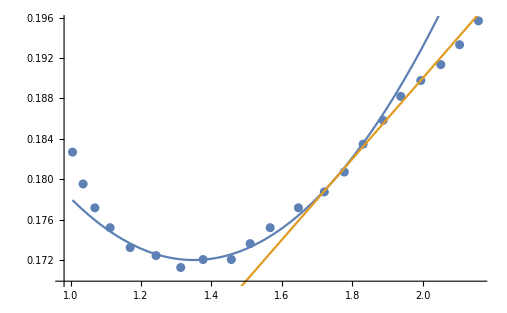

```mathematica
plt51=ListPlot[Transpose@{T5,Cp5}];(*Cp vs temp*)
plt52=Plot[{0.172+0.05*(x-1.35)^2,0.19+0.04(x-2.0)},{x,T5[[1]],T5[[Length[T5]]]}];
Show[plt51,plt52]
```

```mathematica
(*For ϵ=-0.32%*)
```

```mathematica
TvsCp4:={{1.0122494432071272,0.20748031496062994},{1.0489977728285078,0.2035433070866142},{1.0957683741648108,0.2003937007874016},{1.1391982182628064,0.19763779527559058},{1.1959910913140313,0.1956692913385827},{1.2327394209354121,0.1940944881889764},{1.2895322939866372,0.1921259842519685},{1.3596881959910916,0.1921259842519685},{1.4064587973273943,0.19133858267716536},{1.4732739420935412,0.19055118110236222},{1.5334075723830733,0.19173228346456694},{1.5835189309576836,0.1921259842519685},{1.6403118040089089,0.19330708661417326},{1.6737193763919822,0.19330708661417326},{1.7171492204899779,0.19527559055118113}}
```

```mathematica
TvsCp4[[4]][[1]]
```

1.1392

```mathematica
Length[TvsCp4]
```

15

```mathematica
T4=Range[Length[TvsCp4]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

```mathematica
Cp4=Range[Length[TvsCp4]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

```mathematica
For[i=1,i<=Length[TvsCp4],i++,T4[[i]]=TvsCp4[[i]][[1]];Cp4[[i]]=TvsCp4[[i]][[2]]]
```

```mathematica
Length[T4]
```

15

```mathematica
T4
```

{1.01225,1.049,1.09577,1.1392,1.19599,1.23274,1.28953,1.35969,1.40646,1.47327,1.53341,1.58352,1.64031,1.67372,1.71715}

```mathematica
Cp4
```

{0.20748,0.203543,0.200394,0.197638,0.195669,0.194094,0.192126,0.192126,0.191339,0.190551,0.191732,0.192126,0.193307,0.193307,0.195276}

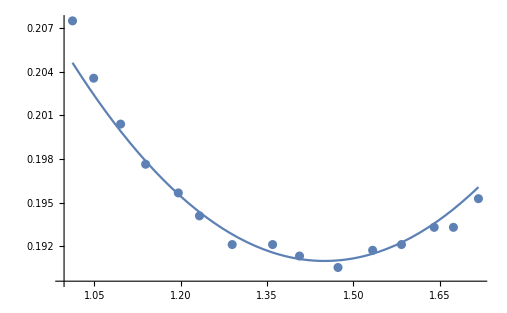

```mathematica
plt41=ListPlot[Transpose@{T4,Cp4}];(*Cp vs temp*)
plt42=Plot[{0.191+0.071*(x-1.45)^2,0.19+0.04(x-2.0)},{x,T4[[1]],T4[[Length[T4]]]}];
Show[plt41,plt42]
```

```mathematica
(*Overlaying all the plots*)
```

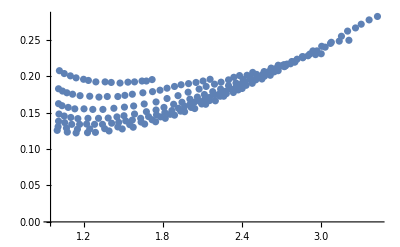

```mathematica
Show[plt101,plt91,plt81,plt71,plt61,plt51,plt41(**)](*The plot form 10 to 4 correspond to increaseing Cp's*)
```